# Paper Diagram

HMSC

Creating the diagram that will be used for the first publication

## First Tests

GraphTransitionsFrequenciesWithMax::shdw: Symbol GraphTransitionsFrequenciesWithMax appears in multiple contexts {PajaroLocoPublic`,Global`}; definitions in context PajaroLocoPublic` may shadow or be shadowed by other definitions.

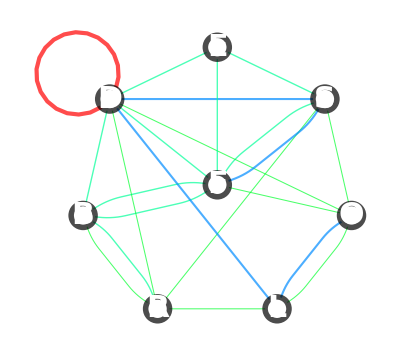

```mathematica
<<PajaroLocoPublic`
matrix={
{0,1,0,0,0,1,0,1},
{1,0,1,0,0,0,0,1},
{0,1,0,1,0,1,0,1},
{0,0,0,0,1,0,0,1},
{1,0,0,1,0,1,0,1},
{1,0,0,0,0,0,0,1},
{1,0,0,0,0,1,0,1},
{0,0,0,0,0,0,0,1}
};
markov=matrix/(Total/@matrix);
(*markov=ReplacePart[markov,{i_,i_}->0];*)
labels={"F","B","R","L","O","S","E","D"};
(*Network*)
edgeshape[e_,___]:={Arrowheads[{{.035,.35}}],Arrow[e]}
GraphTransitionsFrequenciesWithMax[{markov,labels},1,
VariableStyle->"Both",
EdgeShapeFunction->edgeshape,
LineThickness->.0075,
VertexSize->.2,
VertexLabelStyle->Directive[{30,Italic,Bold}],
GraphLayout->"StarEmbedding",
VertexStyle->Directive[{White,EdgeForm[Thickness[.01]]}]
]
```

```mathematica
<<PajaroLocoPublic`
matrix={
{0,1,0,0,0,1,1},
{1,0,1,0,0,0,1},
{0,1,0,1,0,1,1},
{0,0,0,0,1,0,1},
{1,0,0,1,0,1,1},
{1,0,0,0,0,0,1},
{0,0,0,0,0,0,1}
};
markov=matrix/(Total/@matrix);
(*markov=ReplacePart[markov,{i_,i_}->0];*)
labels={"F","B","R","L","O","S","D"};
(*Network*)
edgeshape[e_,___]:={Arrowheads[{{.035,.35}}],Arrow[e]}
GraphTransitionsFrequenciesWithMax[{markov,labels},1,
VariableStyle->"Both",
EdgeShapeFunction->edgeshape,
LineThickness->.0075,
VertexSize->.2,
ImageSize->1000,
VertexLabelStyle->Directive[{10,Italic,Bold}],
GraphLayout->"StarEmbedding",
VertexStyle->Directive[{White,EdgeForm[Thickness[.01]]}],
VertexCoordinates->{{5,0},{3,4},{4,5},{6,7},{9,0},{10,2},{0,0}}
];
```

```mathematica
PolarToRectangular[r_,θ_]:={r*Cos[θ],r*Sin[θ]}
```

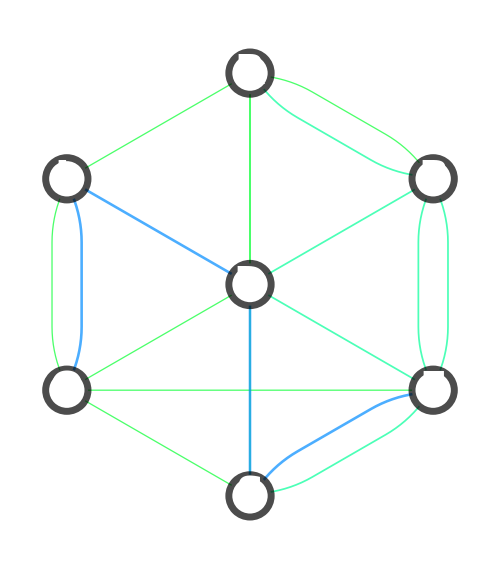

```mathematica
<<PajaroLocoPublic`
matrix={
{0,1,0,0,0,1,1},
{1,0,1,0,0,0,1},
{0,1,0,1,0,1,1},
{0,0,0,0,1,0,1},
{1,0,0,1,0,1,1},
{1,0,0,0,0,0,1},
{0,0,0,0,0,0,1}
};
markov=matrix/(Total/@matrix);
markov=ReplacePart[markov,{i_,i_}->0];
labels={"F","B","R","L","O","S","D"};
(*Network*)
rotation=-π/6;
delta=2π/(Length[matrix]-1);
polars=Range[0+rotation,rotation+2π-delta,delta];
coords=Append[PolarToRectangular[10,#]&/@polars,{0,0}];
edgeshape[e_,___]:={Arrowheads[{{.035,.35}}],Arrow[e]}
GraphTransitionsFrequenciesWithMax[{markov,labels},1,
VariableStyle->"Both",
EdgeShapeFunction->edgeshape,
LineThickness->.0075,
VertexSize->.2,
ImageSize->500,
VertexLabelStyle->Directive[{40,Italic,Bold}],
GraphLayout->"StarEmbedding",
VertexStyle->Directive[{White,EdgeForm[Thickness[.01]]}],
VertexCoordinates->coords
]
```

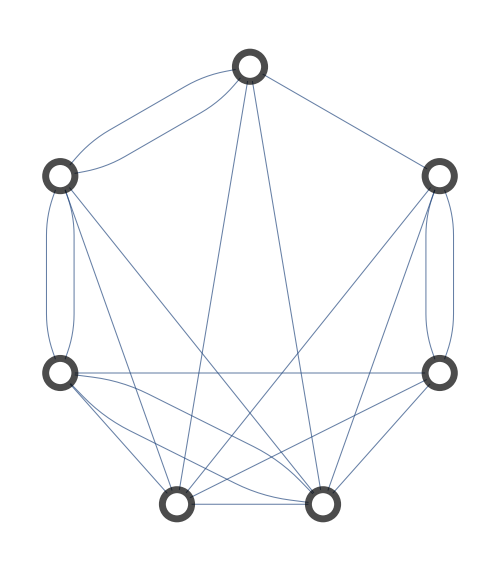

```mathematica
<<PajaroLocoPublic`
matrix={
{0,1,0,0,0,1,1},
{1,0,1,0,0,1,1},
{0,1,0,1,0,1,1},
{0,0,0,0,1,1,1},
{1,0,0,1,0,1,1},
{1,0,0,0,0,0,1},
{0,0,0,0,0,0,1}
};
markov=matrix/(Total/@matrix);
markov=ReplacePart[markov,{i_,i_}->0];
labels={"F","B","R","L","O","S","D"};
(*Network*)
rotation=-π/6;
delta=2π/(Length[matrix]-1);
polars=Range[0+rotation,rotation+2π-delta,delta];
coords=Append[PolarToRectangular[15,#]&/@polars,{0,0}];
{p1,p2,p3,p4,p5,p6,p7}=coords;
coords={(*p5*){-(15 √3)/2,-15/2.5},p4,p3,p2,{(15 √3)/2,-15/2.5}(*p1*),{5,-15},{-5,-15}};
edgeshape[e_,___]:={Arrowheads[{{.035,.35}}],Arrow[e]}
GraphTransitionsFrequenciesWithMax[{markov,labels},1,
VariableStyle->"None",
EdgeShapeFunction->edgeshape,
LineThickness->.0015,
VertexSize->.2,
ImageSize->500,
VertexLabelStyle->Directive[{20,Italic,Bold}],
GraphLayout->"StarEmbedding",
VertexStyle->Directive[{White,EdgeForm[Thickness[.01]]}],
VertexCoordinates->coords
]
```

## Final Version

### Functions

```mathematica
VertexNumberToVertexSyllable[syllables_,fixedEdgesList_]:=Table[DirectedEdge[syllables[[fixedEdgesList[[index]][[1]][[1]]]],syllables[[fixedEdgesList[[index]][[1]][[2]]]]->fixedEdgesList[[index]][[2]]]//N,{index,1,Length[fixedEdgesList]}]
Options[EdgesStyleList2]:={LineThickness->.004,VariableStyle->"Both"}
EdgesStyleList2[vertexSyllableList_,OptionsPattern[]]:=Switch[OptionValue[VariableStyle],"LineColor",Table[DirectedEdge[vertexSyllableList[[i]][[1]][[1]],vertexSyllableList[[i]][[1]][[2]]]->{Hue[.85*vertexSyllableList[[i]][[2]]+.15],Thickness[OptionValue[LineThickness]]},{i,1,Length[vertexSyllableList]}],"LineWidth",Table[DirectedEdge[vertexSyllableList[[i]][[1]][[1]],vertexSyllableList[[i]][[1]][[2]]]->{Black,Thickness[vertexSyllableList[[i]][[2]]*OptionValue[LineThickness]]},{i,1,Length[vertexSyllableList]}],"Both",Table[DirectedEdge[vertexSyllableList[[i]][[1]][[1]],vertexSyllableList[[i]][[1]][[2]]]->{Hue[.85*vertexSyllableList[[i]][[2]]+.15],Thickness[vertexSyllableList[[i]][[2]]*OptionValue[LineThickness]]},{i,1,Length[vertexSyllableList]}],_,Table[DirectedEdge[vertexSyllableList[[i]][[1]][[1]],vertexSyllableList[[i]][[1]][[2]]]->{Thickness[OptionValue[LineThickness]]},{i,1,Length[vertexSyllableList]}]]
edgeshape[e_,___]:={Arrowheads[{{.015,.9}}],Arrow[e]}
PolarToRectangular[r_,θ_]:={r*Cos[θ],r*Sin[θ]}

Options[GraphTransitionsFrequenciesWithMax]:={VertexStyle->Automatic,VertexCoordinates->Automatic,LineThickness->.0075,VariableStyle->"Both",GraphLayout->Automatic,ImageSize->Automatic,VertexSize->.5,EdgeShapeFunction->edgeshape,VertexLabelStyle->{Italic},EdgeStyle->{Thick}}
GraphTransitionsFrequenciesWithMax[frequenciesOutput_,max_,OptionsPattern[]]:=Module[{frequencies,syllables,edges,fixedEdgesList,vertexSyllableList,normalizedVertexSyllableList,edgesStyleList,links},frequencies=frequenciesOutput[[1]];
syllables=frequenciesOutput[[2]];
edges=Table[DirectedEdge[i,j]->frequencies[[i,j]],{i,Length[syllables]},{j,Length[syllables]}]//Flatten;
fixedEdgesList=DeleteCases[edges,DirectedEdge[_,_]->0];
vertexSyllableList=VertexNumberToVertexSyllable[frequenciesOutput[[2]],fixedEdgesList];
normalizedVertexSyllableList=(DirectedEdge[#[[1]],#[[2]][[1]]]->#[[2]][[2]]/max&)/@vertexSyllableList;
edgesStyleList=EdgesStyleList2[normalizedVertexSyllableList,LineThickness->OptionValue[LineThickness],VariableStyle->OptionValue[VariableStyle]];
links=DirectedEdge[#[[1]],#[[2,1]]]&/@vertexSyllableList;
Print[edgesStyleList];
Graph[syllables,links,EdgeWeight->vertexSyllableList[[All,2,2]],VertexStyle->OptionValue[VertexStyle],EdgeStyle->OptionValue[EdgeStyle],VertexCoordinates->OptionValue[VertexCoordinates],ImageSize->OptionValue[ImageSize],GraphLayout->OptionValue[GraphLayout],EdgeShapeFunction->OptionValue[EdgeShapeFunction],VertexSize->OptionValue[VertexSize],VertexLabelStyle->OptionValue[VertexLabelStyle],VertexLabels->Placed["Name",Center],EdgeLabels->Table[links[[i]]->Placed[fixedEdgesList[[All,2]][[i]],Tooltip],{i,Length[links]}]]
]
```

### Generation

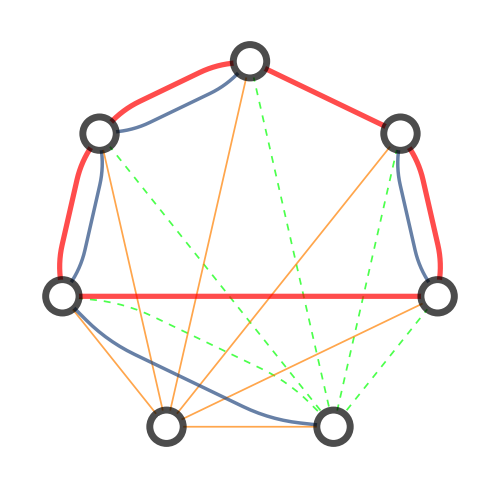

```mathematica
matrix={
{0,10,0,0,0,1,1},
{1,0,1,0,0,1,1},
{0,1,0,1,0,1,1},
{0,0,0,0,1,1,1},
{1,0,0,1,0,1,1},
{1,0,0,0,0,0,1},
{0,0,0,0,0,0,1}
};
markov=matrix/(Total/@matrix);
{colorA,colorB,colorC,colorD}={Red,Blue,Green,Orange};
{ThicknessA,ThicknessB,ThicknessC,ThicknessD}={.0075,.005,.0025,.0025};
edgeshape[e_,___]:={Arrowheads[{{.05,.75}}],Arrow[e]}
markov=ReplacePart[markov,{i_,i_}->0];
labels={"F","B","R","L","O","S","D"};
(*Network*)
delta=2π/(Length[matrix]);
rotation=2.75delta;
polars=Range[0+rotation,rotation+2π-delta,delta];
coords=PolarToRectangular[15,#]&/@polars;
{p1,p2,p3,p4,p5,p6,p7}=coords;
coords={p2,p1,p7,p6,p5,p4,p3};
GraphTransitionsFrequenciesWithMax[{markov,labels},1,
VariableStyle->"None",
EdgeShapeFunction->edgeshape,
LineThickness->.0015,
VertexSize->.2,
ImageSize->500,
VertexLabelStyle->Directive[{25,Italic,Bold}],
GraphLayout->"StarEmbedding",
VertexStyle->Directive[{White,EdgeForm[Thickness[.01]]}],
VertexCoordinates->coords,
EdgeStyle->{
"F"->"B"->{colorA,Thickness[ThicknessA]},"F"->"S"->{Dashed,Thickness[ThicknessC],colorC},"F"->"D"->{Thickness[ThicknessD],colorD},"B"->"F"->{Thickness[ThicknessB]},"B"->"R"->{colorA,Thickness[ThicknessA]},"B"->"S"->{Dashed,Thickness[ThicknessC],colorC},"B"->"D"->{Thickness[ThicknessD],colorD},"R"->"B"->{Thickness[ThicknessB]},"R"->"L"->{colorA,Thickness[ThicknessA]},"R"->"S"->{Dashed,Thickness[ThicknessC],colorC},"R"->"D"->{Thickness[ThicknessD],colorD},"L"->"O"->{Thickness[ThicknessA],colorA},"L"->"S"->{Dashed,Thickness[ThicknessC],colorC},"L"->"D"->{Thickness[ThicknessD],colorD},"O"->"F"->{Thickness[ThicknessA],colorA},"O"->"L"->{Thickness[ThicknessB]},"O"->"S"->{Dashed,Thickness[ThicknessC],colorC},"O"->"D"->{Thickness[ThicknessD],colorD},"S"->"F"->{Thickness[ThicknessB]},"S"->"D"->{Thickness[ThicknessD],colorD}
}
]
```